## Generating 5-fold symmetry axis on 2D surface

n= 1

```mathematica
a1 = Cos[2π/5];
b1 = Cos[π/5];
c1 = Sin[2π/5];
d1 = Sin[4π/5];
vertices={{a1,-c1}, {1,0}, {a1,c1}, {-b1,d1}, {-b1,-d1}};
transv1 = {{a1+1,-c1}, {1+1,0}, {a1+1,c1}, {-b1+1,d1}, {-b1+1,-d1}};
```

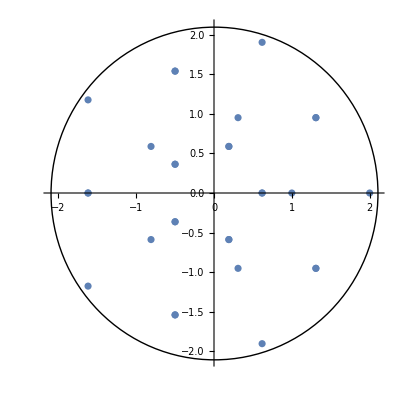

```mathematica
rotv1 = RotationTransform[2π/5, {0,0}] /@ # &@transv1;
rotv2 = RotationTransform[2π/5, {0,0}] /@ # &@rotv1;
rotv3 = RotationTransform[2π/5, {0,0}] /@ # &@rotv2;
rotv4 = RotationTransform[2π/5, {0,0}] /@ # &@rotv3;
n1point = ListPlot[Join[vertices, transv1, rotv1, rotv2, rotv3, rotv4], AspectRatio->1];
circle = Graphics[Circle[{0, 0}, 2.1]];
n1 = Show[n1point, circle, PlotRange-> All]
```

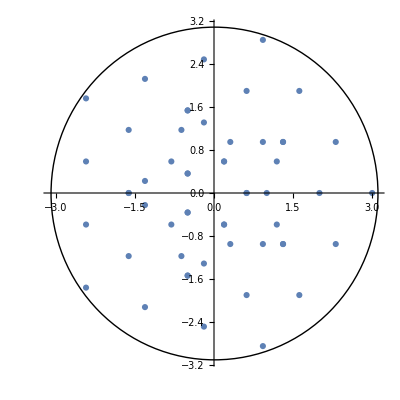

```mathematica
a1 = Cos[2π/5];
b1 = Cos[π/5];
c1 = Sin[2π/5];
d1 = Sin[4π/5];
vertices={{a1,-c1}, {1,0}, {a1,c1}, {-b1,d1}, {-b1,-d1}};
transv1 = {{a1+1,-c1}, {1+1,0}, {a1+1,c1}, {-b1+1,d1}, {-b1+1,-d1}};
rotv1 = RotationTransform[2π/5, {0,0}] /@ # &@transv1;
rotv2 = RotationTransform[2π/5, {0,0}] /@ # &@rotv1;
rotv3 = RotationTransform[2π/5, {0,0}] /@ # &@rotv2;
rotv4 = RotationTransform[2π/5, {0,0}] /@ # &@rotv3;
transv2 = {{a1+2,-c1}, {1+2,0}, {a1+2,c1}, {-b1+2,d1}, {-b1+2,-d1}};
rotv5 = RotationTransform[2π/5, {0,0}] /@ # &@transv2;
rotv6 = RotationTransform[2π/5, {0,0}] /@ # &@rotv5;
rotv7 = RotationTransform[2π/5, {0,0}] /@ # &@rotv6;
rotv8 = RotationTransform[2π/5, {0,0}] /@ # &@rotv7;
n2point = ListPlot[Join[vertices, transv1, rotv1, rotv2, rotv3, rotv4, transv2, rotv5, rotv6, rotv7, rotv8], AspectRatio->1];
circle2 = Graphics[Circle[{0, 0}, 3.1]];
n2 = Show[n2point, circle2, PlotRange-> All]
```

## Loading data

import data as string:

```mathematica
data =Import[URLDownload["https://files.rcsb.org/download/1JS9.pdb1.gz"],"String"];
```

replace negative signs(-) with spaces to separate columns:

```mathematica
spaced  = StringReplace[data,"-"-> " -"];
```

export modified file to directory as text:

```mathematica
Export["/Users/Jihyeon/Desktop/3j3i_spaced.txt",spaced];
```

open modified file:

```mathematica
str = OpenRead["/Users/Jihyeon/Desktop/3j3i_spaced.txt"];
```

Read data starting from row 180:

```mathematica
Do[Read[str,"String"],181]
```

```mathematica
Read[str,"String"]
```

ATOM      1  N   LYS A  41      71.779  -11.151  76.910  1.00168.69           N

read the list as words

```mathematica
fullrecord=ReadList[str,"Word", RecordLists->True];
```

split the list when consecutive first letter appears:

```mathematica
splitted = Split[fullrecord,First[#1]===First[#2]&];
```

remove unnecessary rows:

```mathematica
removed = DeleteCases[splitted,x_/;First[First[x]]== "TER"];
removed = DeleteCases[removed,x_/;First[First[x]]== "HETATM"];
removed = DeleteCases[removed,x_/;First[First[x]]== "MODEL"];
removed = DeleteCases[removed,x_/;First[First[x]]== "ENDMDL"];
removed = DeleteCases[removed,x_/;First[First[x]]== "MASTER"];
removed = DeleteCases[removed,x_/;First[First[x]]== "END"];
```

```mathematica
Dimensions[removed]
```

{180}

## Calculating center of mass

### extracting coordinates

only extract atom data and coordinates:

```mathematica
atom =   removed⟦All,All, -1⟧;
```

replace atoms with its atomic mass:

```mathematica
mass = atom/.{"N"->14.00, "C" -> 12.01, "O" -> 15.99, "S" -> 32.06};
```

extract x,y,z coordinates:

```mathematica
xcoor =  ToExpression[removed⟦All,All, 7⟧]
```

{1}
 |  |  |  |

```mathematica
ycoor =  ToExpression[removed⟦All,All, 8⟧]
```

{1}
 |  |  |  |

```mathematica
zcoor =  ToExpression[removed⟦All,All, 9⟧]
```

{1}
 |  |  |  |

```mathematica
chain = removed⟦All,All, 5⟧
```

{1}
 |  |  |  |

### Calculation

equation for calculating center of mass:

```mathematica
calcx[mass_,xcoor_] :=Sum[mass[[i]]* xcoor[[i]], {i, Length[mass]}]  /Sum[mass[[i]],{ i, Length[mass]}]
```

```mathematica
xset = MapThread[calcx, {mass, xcoor}];
```

```mathematica
calcy[mass_,ycoor_] :=Sum[mass[[i]]* ycoor[[i]], {i, Length[mass]}]  /Sum[mass[[i]],{ i, Length[mass]}]
```

```mathematica
yset = MapThread[calcy, {mass, ycoor}];
```

```mathematica
calcz[mass_,zcoor_] :=Sum[mass[[i]]* zcoor[[i]], {i, Length[mass]}]  /Sum[mass[[i]],{ i, Length[mass]}]
```

```mathematica
zset = MapThread[calcz, {mass, zcoor}];
```

put all x, y, z coordinates together:

```mathematica
totcoor[xset_,yset_,zset_] :=List[xset, yset, zset]
centercoor = MapThread[totcoor, {xset, yset, zset}];
```

## Graphing points in 3D

```mathematica
flatchain = Flatten@chain;
```

```mathematica
x = Flatten[xcoor];
y = Flatten[ycoor];
z = Flatten[zcoor];
```

```mathematica
totcoor[x_,y_,z_] :=List[x, y, z]
allcoor = MapThread[totcoor, {x, y, z}];
```

```mathematica
colorlist = ToExpression[flatchain/.{"A"-> "Blue", "B" -> "Pink", "C" -> "Green", "D" -> "Red"}];
```

```mathematica
Graphics3D[{Point[allcoor,VertexColors->colorlist]}, Lighting->Automatic]
```

-Graphics3D-

```mathematica
chaintype = First /@ chain;
```

```mathematica
colorlist2 = ToExpression[chaintype/.{"A"-> "Blue", "B" -> "Pink", "C" -> "Green", "D" -> "Red"}];
```

```mathematica
Graphics3D[{Point[centercoor,VertexColors->colorlist2]}]
```

-Graphics3D-

```mathematica
ListSurfacePlot3D[centercoor, BoxRatios->{1, 1, 1}]
```

-Graphics3D-

## Tiling

```mathematica
MaxCellMeasure
```

```mathematica
Mesh
```

```mathematica
Tally[Length/@%82]
```

{{13,23},{12,52},{10,12},{11,26},{9,3}}

```mathematica
Names["Mesh*"]
```

{Mesh,MeshCellCentroid,MeshCellCount,MeshCellHighlight,MeshCellIndex,MeshCellLabel,MeshCellMarker,MeshCellMeasure,MeshCellQuality,MeshCells,MeshCellShapeFunction,MeshCellStyle,MeshCoordinates,MeshFunctions,MeshPrimitives,MeshQualityGoal,MeshRange,MeshRefinementFunction,MeshRegion,MeshRegionQ,MeshShading,MeshStyle}

```mathematica
MeshCells[cm,2]
```

```mathematica
MeshCoordinates[cm]
```

```mathematica
cm["MeshConnectivity"]
```

{{45,42,43},{8,57,9},{21,27,26},{50,5,4},{40,39,20},{5,34,1},{5,1,4},{14,45,15},{32,33,35},{17,29,28},{42,3,43},{39,37,38},{57,51,9},{29,27,28},{40,59,36},{37,36,31},{33,34,35},{34,7,1},{13,14,12},{8,7,33},{32,59,58},{56,57,60},{27,21,54},{57,56,51},{27,53,28},{2,3,1},{42,45,41},{59,57,58},{56,19,52},{19,18,52},{59,32,36},{29,17,11},{14,11,12},{27,29,30},{29,15,30},{50,4,46},{57,59,60},{59,40,60},{19,20,18},{37,48,38},{2,1,6},{57,8,58},{51,55,9},{7,34,33},{18,53,52},{4,42,46},{21,25,54},{55,10,9},{11,17,16},{21,26,22},{48,13,38},{40,20,60},{29,11,15},{8,33,58},{11,14,15},{34,5,35},{15,45,30},{45,44,30},{53,51,52},{55,25,10},{20,19,60},{19,56,60},{35,50,49},{25,21,23},{10,25,24},{14,13,47},{33,32,58},{1,3,4},{3,42,4},{26,44,22},{1,7,6},{3,23,43},{23,22,43},{22,44,43},{36,32,31},{32,35,31},{25,55,54},{37,39,36},{39,40,36},{5,50,35},{25,23,24},{20,17,18},{17,28,18},{55,53,54},{53,27,54},{53,55,51},{17,20,16},{20,39,16},{44,26,30},{26,27,30},{47,13,48},{23,2,24},{21,22,23},{7,8,6},{8,10,6},{3,2,23},{44,45,43},{50,46,49},{46,47,49},{10,8,9},{39,12,16},{12,11,16},{13,12,38},{12,39,38},{28,53,18},{45,14,41},{14,47,41},{51,56,52},{47,46,41},{46,42,41},{2,6,24},{6,10,24},{47,48,49},{48,37,49},{37,31,49},{31,35,49}}

```mathematica
cm["Properties"]
```

```mathematica
cm = DiscretizeRegion[ConvexHullMesh[centercoor],MaxCellMeasure->Infinity]
```

-Graphics3D-

```mathematica
MeshPrimitives[cm,2]
```

```mathematica
{pts,tetrahedra}=TetGenDelaunay[centercoor]
```

```mathematica
MeshPrimitives[cm,4]
```

{}

```mathematica
center = RegionCentroid[cm]
```

{0.0000223054,-0.0000181183,0.0000394123}

```mathematica
Map[Line[{#, center]&, centercoor]
```

```mathematica
mesh = TriangulateMesh@ConvexHullMesh@centercoor
-Graphics3D-
Tally[MeshPrimitives[mesh,2]/.Polygon->Length]
{{3,10704}}
```

#### Calculating normal vector

```mathematica
p1 = {1,2,3};
p2 = {2,2,3};
p3 = {4,2,1};
```

```mathematica
normal[p1_,p2_,p3_] :=
(vx =p2[[1]]-p1[[1]]
vy = p2[[2]]-p1[[2]];
vz = p2[[3]]-p1[[3]];
wx = p3[[1]]-p1[[1]] ;
wy = p3[[2]]-p1[[2]] ;
wz =p3[[3]]-p1[[3]] ;
nx = N[vy*wz-vz* wy];
ny = N[vz *wx-vx * wz];
nz = N[vx*wy-vy*wx];
ax = nx/(Abs[nx]+Abs[ny]+Abs[nx]);
ay = ny/(Abs[nx]+Abs[ny]+Abs[nz]);
az = nz/(Abs[nx]+Abs[ny]+Abs[nz]);
List[{ax,ay,az}])
```

```mathematica
normal[p1,p2,p3]
```